{-1.12918,{x→-22.882,y→-24.8596}}

{1.11022×10^-16,{x→-22.882,y→-24.8596}}

{3.16856,{x→9.55817,y→6.0316}}

{1.,{x→9.55817,y→6.0316}}

{3.50387×10^-17,{x→-22.882,y→-24.8596}}

-Graphics3D-

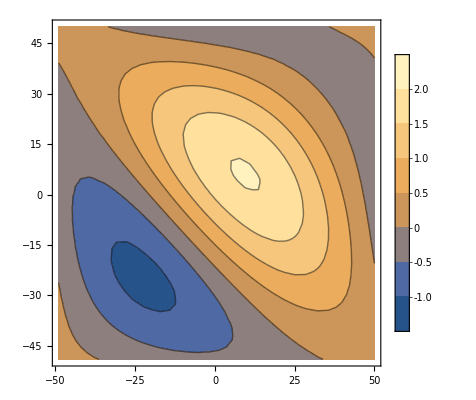

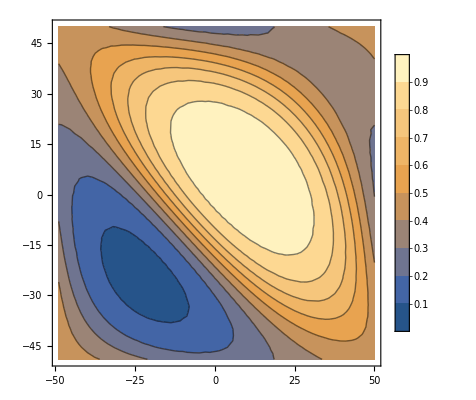

```mathematica
Clear[A0,A1,A2,A3,B0,B1,B2,B3,kx,ky,kmax,x,y,F,FS,min,max,F1,F2]
L=100;
(*A0=-0.04; A1=-0.012584; A2=0.010560; A3=0.321488;
B0=0; B1=0.423176; B2=0.355412; B3=0.422710; *)
A0=0.27404301; A1=0.39766882; A2=0.34173524; A3=0.55832963;
B1=0.36650368; B2=0.46845851; B3=0.48469572;
F=A0 Cos[0]+A1 Cos[2 π y/L]+A2 Cos[2 π x/L]+ A3 Cos[2 π (x+y)/L]+B1 Sin[2 π y/L]+B2 Sin[2 π x/L]+B3 Sin[2 π (x+y)/L];
min=NMinimize[{F && Abs[x]<=50 && Abs[y]<=50},{x,y}]
F1=F-min[[1]];
NMinimize[{F1 && Abs[x]<=50 && Abs[y]<=50},{x,y}]
max=NMaximize[{F1 && Abs[x]<=50 && Abs[y]<=50},{x,y}]
F2=F1/max[[1]];
NMaximize[{F2 && Abs[x]<=50 && Abs[y]<=50},{x,y}]
NMinimize[{F2 && Abs[x]<=50 && Abs[y]<=50},{x,y}]
Plot3D[F,{x,-49,50},{y,-49,50},PlotLegends->Automatic]
FS=1/(1+Exp[-2.0 (F-0.2)]);
ContourPlot[F,{x,-49,50},{y,-49,50},PlotLegends->Automatic]
ContourPlot[FS,{x,-49,50},{y,-49,50},PlotLegends->Automatic]
```

```mathematica
Clear[A00,A11,A01,A10,B00,B11,B01,B10,x,y,L,F,Fx,Fy,F1,F2,max1]

L=100;
p=22.0/7.0;
F=A00+A00 Cos[2 p y/L]+B01 Sin[2 p y/L]+A00 Cos[2 p x/L]+B01 Sin[2 p x/L]+A00 Cos[2 p (x+y)/L]+B01 Sin[2 p (x+y)/L];
A00=-0.09217604; A01=-0.08181521; A10=-0.03904768; A11=0.40433327;
B01=0.42206520; B10=0.38018330; B11=0.46585211;
F=A00+A00 Cos[2 p y/L]+B01 Sin[2 p y/L]+A00 Cos[2 p x/L]+B01 Sin[2 p x/L]+A00 Cos[2 p (x+y)/L]+B01 Sin[2 p (x+y)/L];max=FindMaximum[{F && Abs[x]<=50 && Abs[y]<=50},{x,y}]


(*max=FindMaximum[{F && Abs[x]<=50 && Abs[y]<=50},{x,y}];
min=FindMinimum[{F && Abs[x]<=50 && Abs[y]<=50},{x,y}]
x0=max[[2,1,2]];
y0=max[[2,2,2]];
x1=min[[2,1,2]]
y1=min[[2,2,2]]
F1=F-min[[1]];
FindMinimum[{F1 && Abs[x]<=50 && Abs[y]<=50},{{x,x1},{y,y1}}]
max1=FindMaximum[{F1 && Abs[x]<=50 && Abs[y]<=50},{{x,x0},{y,y0}}];
max1[[1]];
F2=F1/max1[[1]];
FindMaximum[{F2 && Abs[x]<=50 && Abs[y]<=50},{{x,x0},{y,y0}}]
FindMinimum[{F2 && Abs[x]<=50 && Abs[y]<=50},{{x,x1},{y,y1}}]*)
(*A00=-0.005230; A01=0.012770; A10=0.003184; A11=0.381302;
B00=0.410231; B01=0.395711; B10=0.395863; B11=0.384764;
NSolve[{Fx==0,Fy == 0},{x,y}]
x=35.06657715353851; y=34.6800735652011;
F*)
(*Solve[{F==0},{x,y}]*)
```

{0.98094,{x→18.9404,y→18.9404}}

```mathematica
Clear[i,A00,A11,A01,A10,B00,B11,B01,B10,x,y,L,F,Fx,Fy,F1,F2,max1]
L=100;
p=22.0/7.0;
filename="~/Desktop/research/ML/active_matter/field_amp.dat";
strm=OpenRead[filename];
rslts=ReadList[strm,{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
rslts[[3]]
A00=-0.09217604;
B01=0.42206520;F=A00+A00 Cos[2 p y/L]+B01 Sin[2 p y/L]+A00 Cos[2 p x/L]+B01 Sin[2 p x/L]+A00 Cos[2 p (x+y)/L]+B01 Sin[2 p (x+y)/L];max=FindMaximum[{F && Abs[x]<=50 && Abs[y]<=50},{x,y}];
min=FindMinimum[{F && Abs[x]<=50 && Abs[y]<=50},{x,y}];
max[[1]];
F1=F-min[[1]];
max1=FindMaximum[{F1 && Abs[x]<=50 && Abs[y]<=50},{x,y}];
max1[[1]]
```

{3,-0.092176,-0.0818152,-0.0390477,0.404333,0.458747,0.422065,0.380183,0.465852}

2.23904

```mathematica
Clear[i,A00,A11,A01,A10,B00,B11,B01,B10,x,y,L,F,Fx,Fy,F1,F2,max1,NN,x0,y0,x1,y1]
L=100;
p=22.0/7.0;
NN=100000;
filename="~/Desktop/research/ML/active_matter/field_amp01.dat";
strm=OpenRead[filename];
filename1=StringJoin["max_min02.dat"];
strmw=OpenWrite[filename1];
rslts=ReadList[strm,{Number,Number,Number,Number,Number,Number,Number,Number,Number}];
rslts[[3]];
rslts[[3,2]];
For[i=1,i≤NN,i++,A00=rslts[[i,2]];A01=rslts[[i,3]];A10=rslts[[i,4]];A11=rslts[[i,5]];B00=rslts[[i,6]];B01=rslts[[i,7]];B10=rslts[[i,8]];B11=rslts[[i,9]];F=A00+A01 Cos[2 p y/L]+B01 Sin[2 p y/L]+A10 Cos[2 p x/L]+B10 Sin[2 p x/L]+A11 Cos[2 p (x+y)/L]+B11 Sin[2 p (x+y)/L];max=NMaximize[{F && Abs[x]<=50 && Abs[y]<=50},{x,y}];
min=NMinimize[{F && Abs[x]<=50 && Abs[y]<=50},{x,y}];
(*x0=max[[2,1,2]];
y0=max[[2,2,2]];
x1=min[[2,1,2]];
y1=min[[2,2,2]];*)
F1=F-min[[1]];
max1=NMaximize[{F1 && Abs[x]<=50 && Abs[y]<=50},{x,y}];WriteString[strmw,i," ",NumberForm[min[[1]],{13,12}]," ",NumberForm[max1[[1]],{13,12}],"\n"]]
Close[strmw]
Close[strm]
```